```mathematica
LargeDensity=(8750000-6500000)/22500;
OverallDurationSum=Import[NotebookDirectory[]<>"scaled_overall_duration_sum.csv","CSV"];
h2[k_,p_,h1_]:=Max[0,(-Log[1/k]+h1 Log[p])/Log[p]];
```

#### Productivity

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

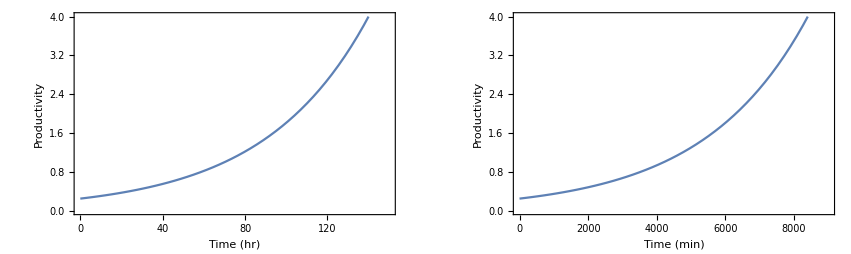

```mathematica
Productivity[h_]:=0.25*1.02^h;
GraphicsArray[{
Plot[Productivity[h],{h,0,150}, Frame->True, PlotRange->{0,4},FrameLabel->{"Time (hr)", "Productivity"}],
Plot[Productivity[m/60],{m,0,9000}, Frame->True, PlotRange->{0,4},FrameLabel->{"Time (min)", "Productivity"}]}]
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

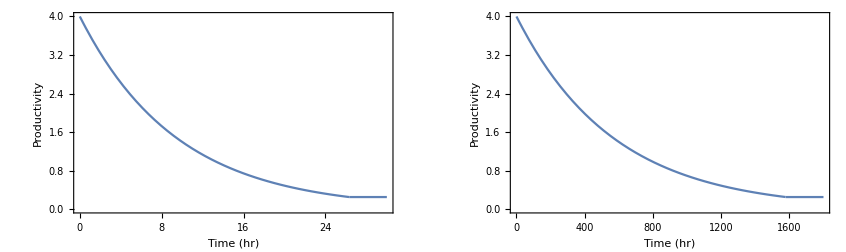

```mathematica
GraphicsArray[{
Plot[Max[4*0.9^h,0.25],{h,0,30}, Frame->True, PlotRange->{0,4},FrameLabel->{"Time (hr)", "Productivity"}],
Plot[Max[4*0.9^(m/60),0.25],{m,0,1800}, Frame->True, PlotRange->{0,4},FrameLabel->{"Time (hr)", "Productivity"}]}]
```

#### Maximal toy duration can be used within that size

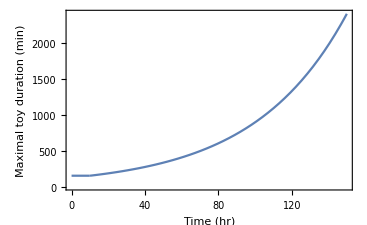

```mathematica
MaximalToyDuration[m_]:=Max[150,600*0.25*1.02^(m-10)];
Plot[MaximalToyDuration[m],{m,0,150}, Frame->True, PlotRange->{0,2400},FrameLabel->{"Time (hr)", "Maximal toy duration (min)"}]
```

#### Compensation toy distribution

Since the largest toys (duration ~ 22500) will always end up with a productivity rate 0.25, we can use the small toys to raise that rate, and then produce large toys w/ productivity rate >0.25, hence save time. 
Therefore, the problem turns to be, how to distribute the small toys, so we can save more time on the large toys (comparing to produce all of them in the productivity rate 0.25).
Use calculus of variations, in case assuming that the available “small” toy duration sum is a constant.

```mathematica
Δh[k_,p_,h_,h1_]:=(1/(1/4)-1/(1/4*p^h1))+k(1/(1/4)-1/(1/4*p^(h-h1)));
```

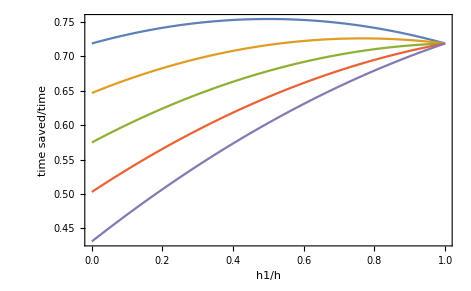

```mathematica
Plot[{
Δh[1,1.02,h,h*h1overh]/.h->10,
Δh[0.9,1.02,h,h*h1overh]/.h->10,
Δh[0.8,1.02,h,h*h1overh]/.h->10,
Δh[0.7,1.02,h,h*h1overh]/.h->10,
Δh[0.6,1.02,h,h*h1overh]/.h->10,
},{h1overh,0,1},Frame->True, FrameLabel->{"h1/h", "time saved/time"}]
```

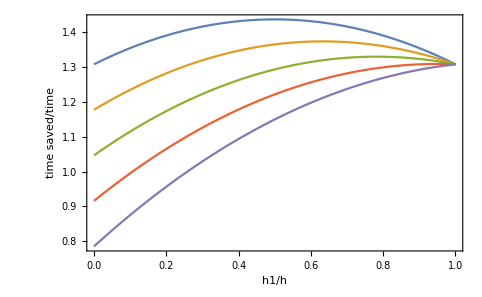

```mathematica
Plot[{
Δh[1,1.02,h,h*h1overh]/.h->20,
Δh[0.9,1.02,h,h*h1overh]/.h->20,
Δh[0.8,1.02,h,h*h1overh]/.h->20,
Δh[0.7,1.02,h,h*h1overh]/.h->20,
Δh[0.6,1.02,h,h*h1overh]/.h->20,
},{h1overh,0,1},Frame->True, FrameLabel->{"h1/h", "time saved/time"}]
```

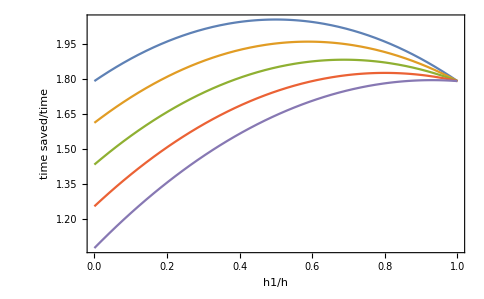

```mathematica
Plot[{
Δh[1,1.02,h,h*h1overh]/.h->30,
Δh[0.9,1.02,h,h*h1overh]/.h->30,
Δh[0.8,1.02,h,h*h1overh]/.h->30,
Δh[0.7,1.02,h,h*h1overh]/.h->30,
Δh[0.6,1.02,h,h*h1overh]/.h->30,
},{h1overh,0,1},Frame->True, FrameLabel->{"h1/h", "time saved/time"}]
```

```mathematica
D[Δh[k,p,h,h1], h1]
```

4 p^-h1 Log[p]-4 k p^(-h+h1) Log[p]

```mathematica
Solve[4 p^-h1 Log[p]-4 k p^(-h+h1) Log[p]==0, h1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{h1→(Log[1/k]+h Log[p])/(2 Log[p])}}

```mathematica
Solve[(Log[1/k]+(h1+h2)Log[p])/(2 Log[p])==h1,h2]
```

{{h2→(-Log[1/k]+h1 Log[p])/Log[p]}}

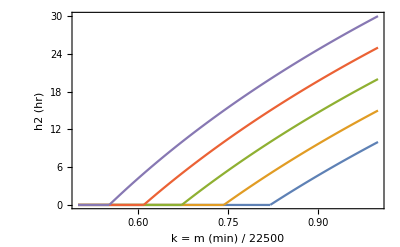

```mathematica
h2[k_,p_,h1_]:=Max[0,(-Log[1/k]+h1 Log[p])/Log[p]];
Plot[{
h2[k,1.02,10],
h2[k,1.02,15],
h2[k,1.02,20],
h2[k,1.02,25],
h2[k,1.02,30],
},{k,0.5,1},Frame->True,PlotRange->{0,30},FrameLabel->{"k = m (min) / 22500","h2 (hr)"}]
```

#### Theoretical packing time before compensation

Naive way, ~ First Available Elf Benchmark 1875730155.0575

```mathematica
(24/10*LargeDensity*∫_0^22500 4*mⅆm)/900*Log[1+900]//N
```

1.83695×10^9

#### Theoretical packing time if the largest possible number of toys start from productivity 0.25

Use all <=600 toys, rectangle distribution:

```mathematica
handleNum=OverallDurationSum[[600]][[2]]/4200/100//N
(24/10*LargeDensity*(∫_0^(22500-handleNum) 4*hⅆh+∫_(22500-handleNum)^22500 1*hⅆh))/900*Log[1+900]//N
```

4284.18

1.36224×10^9

Use all <=2400 toys, rectangle distribution:

```mathematica
handleNum=OverallDurationSum[[2400]][[2]]/8400/100//N
(24/10*LargeDensity*(∫_0^(22500-handleNum) 4*hⅆh+∫_(22500-handleNum)^22500 0.25*hⅆh))/900*Log[1+900]//N
```

2405.79

1.48836×10^9

Use all <=2400 toys, triangle distribution:

```mathematica
Solve[{k*22500+b==8400/60,k*(22500-handleNum*2)+b==0},{k,b}]
```

{{k→0.0290964,b→-514.669}}

```mathematica
(24/10*LargeDensity*∫_0^22500 4/1.02^Max[0, 0.029096 m-514.669]*mⅆm)/900*Log[1+900]//N
```

1.36089×10^9

Theoretical best distrubution

```mathematica
FindRoot[22500*LargeDensity*60∫_0^1 h2[k,1.02,m]ⅆk==OverallDurationSum[[2400]][[2]],{m,30}]
```

{m→44.5808}

```mathematica
(24/10*LargeDensity*∫_0^22500 4/1.02^h2[m/22500,1.02,44.5808]*mⅆm)/900*Log[1+900]//N
```

1.20532×10^9

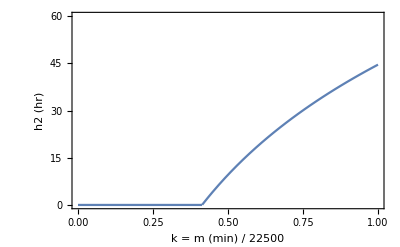

```mathematica
Plot[{
h2[k,1.02,44.5808],
},{k,0,1},Frame->True,PlotRange->{0,60},FrameLabel->{"k = m (min) / 22500","h2 (hr)"}]
```

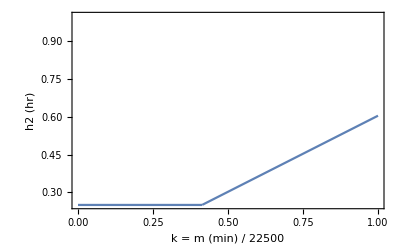

```mathematica
Plot[{
Productivity[h2[k,1.02,44.5808]],
},{k,0,1},Frame->True,PlotRange->{0.25,1},FrameLabel->{"k = m (min) / 22500","h2 (hr)"}]
```

#### Consistency check

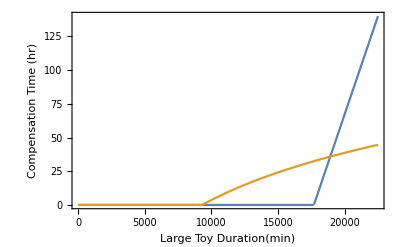

```mathematica
Plot[{
Max[0, 0.029096 m-514.669],
h2[m/22500,1.02,44.5808],
},{m,0,22500},Frame->True,PlotRange->{0,8400/60},FrameLabel->{"Large Toy Duration(min)", "Compensation Time (hr)"}]
```

```mathematica
OverallDurationSum[[2400]][[2]]//N
LargeDensity*60∫_(22500-handleNum)^22500 8400/60 ⅆm
LargeDensity*60∫_0^22500 Max[0, 0.029096 m-514.669]ⅆm
LargeDensity*60∫_0^22500 h2[m/22500,1.02,44.5808]ⅆm
```

2.02087×10^9

2.02087×10^9

2.02064×10^9

2.02087×10^9